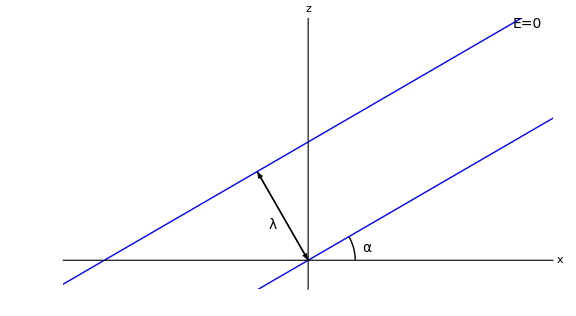

```mathematica
figure=Style[Graphics[{Blue,InfiniteLine[{{0,0},{Cos[30 Degree],Sin[30 Degree]}}],InfiniteLine[{{0,0.5},{Cos[30 Degree],0.5+Sin[30 Degree]}}],
{Black,Arrowheads[0.03],Arrow[{{0,0},{-0.5Sin[30Degree]Cos[30Degree],0.5 Cos[30Degree]Cos[30Degree]}}],Arrow[{{-0.5Sin[30Degree]Cos[30Degree],0.5 Cos[30Degree]Cos[30Degree]},{0,0}}],Text[Style["λ",14],{-0.15,0.15}]},
{Black,Circle[{0,0},0.2,{0,30 Degree}],Text[Style["α",14],{0.25,0.05}]},
{Black,Text[Style["E=0",14],{0.93,1}]}},
Axes->True,AxesOrigin->{0,0},AxesLabel->{"x","z"},Ticks->None,PlotRange->{{-1,1},{-0.1,1}},ImageSize->Large],Antialiasing->False]
```

```mathematica
Export["/tmp/efield-at-angle.png",figure,ImageResolution->500]
```

/tmp/efield-at-angle.png